## NeighborQ-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Sun 11 Jun 2017 11:43:28
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Determine (and display) all the midpoints of all edges in a particular cell on a template

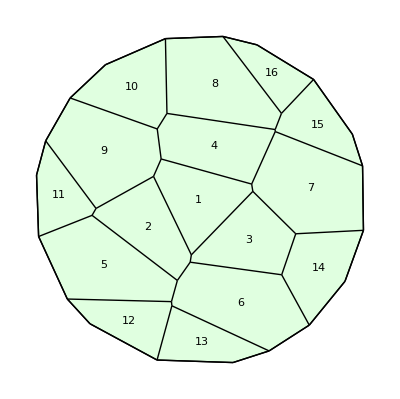

```mathematica
w=TemplateRandomCircularGrid[12,15];
Show[ShowTissue[w, "CellNumbers"-> True]]
```

```mathematica
NeighborQ[w,{6,3}]
```

True

## Connection Matrix * using True/False instead of 1/0

```mathematica
n=NTissueCells[w];
M=Table[NeighborQ[w,{i,j}],{i,1,n},{j,1,n}];
MatrixForm[M]
```

(True | True | True | True | False | False | True | False | True | False | False | False | False | False | False | False
True | True | True | False | True | True | False | False | True | False | True | False | False | False | False | False
True | True | True | False | False | True | True | False | False | False | False | False | False | True | False | False
True | False | False | True | False | False | True | True | True | True | False | False | False | False | True | False
False | True | False | False | True | True | False | False | False | False | True | True | False | False | False | False
False | True | True | False | True | True | False | False | False | False | False | True | True | True | False | False
True | False | True | True | False | False | True | False | False | False | False | False | False | True | True | False
False | False | False | True | False | False | False | True | False | True | False | False | False | False | True | True
True | True | False | True | False | False | False | False | True | True | True | False | False | False | False | False
False | False | False | True | False | False | False | True | True | True | False | False | False | False | False | False
False | True | False | False | True | False | False | False | True | False | True | False | False | False | False | False
False | False | False | False | True | True | False | False | False | False | False | True | True | False | False | False
False | False | False | False | False | True | False | False | False | False | False | True | True | False | False | False
False | False | True | False | False | True | True | False | False | False | False | False | False | True | False | False
False | False | False | True | False | False | True | True | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | True | False | False | False | False | False | False | True | True)